# Bistable networks: kinase with three states

## Finding the condition of multistationarity

Four different states for the Kinase

K1 + S -1> K1S -2> K1 + Sp     
K2 + S -3> K2S -4> K2 + Sp 
K1 -5> K2
K2S -6> K1S
K3 + S -7> K3S -8> K3 + Sp
K2 -9> K3
K3S -10> K2S 
                                   
Sp-11>S  

Species
{S(1), Sp(2), K1 (3) ,K1S (4), K2(5), K2S(6), K3(7), K3S(8) }

```mathematica
ClearAll["Global`*"];
```

```mathematica
A=Table[0,{11},{8}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[4]]=1;
A[[2]][[2]]=1;A[[2]][[3]]=1;A[[2]][[4]]=-1;
A[[3]][[1]]=-1;A[[3]][[5]]=-1;A[[3]][[6]]=1;
A[[4]][[2]]=1;A[[4]][[5]]=1;A[[4]][[6]]=-1;
A[[5]][[3]]=-1;A[[5]][[5]]=1;
A[[6]][[4]]=1;A[[6]][[6]]=-1;
A[[7]][[1]]=-1;A[[7]][[7]]=-1;A[[7]][[8]]=1;
A[[8]][[8]]=-1;A[[8]][[7]]=1;A[[8]][[2]]=1;
A[[9]][[5]]=-1;A[[9]][[7]]=1;
A[[10]][[8]]=-1;A[[10]][[6]]=1;
A[[11]][[2]]=-1;A[[11]][[1]]=1;
stoiM=Transpose[A]
```

{{-1,0,-1,0,0,0,-1,0,0,0,1},{0,1,0,1,0,0,0,1,0,0,-1},{-1,1,0,0,-1,0,0,0,0,0,0},{1,-1,0,0,0,1,0,0,0,0,0},{0,0,-1,1,1,0,0,0,-1,0,0},{0,0,1,-1,0,-1,0,0,0,1,0},{0,0,0,0,0,0,-1,1,1,0,0},{0,0,0,0,0,0,1,-1,0,-1,0}}

```mathematica
ks={Subscript[k, 1]*Subscript[x, 1]*Subscript[x, 3],Subscript[k, 2]*Subscript[x, 4],Subscript[k, 3]*Subscript[x, 1]*Subscript[x, 5],Subscript[k, 4]*Subscript[x, 6],Subscript[k, 5]*Subscript[x, 3],Subscript[k, 6]*Subscript[x, 6],Subscript[k, 7]*Subscript[x, 1]*Subscript[x, 7],Subscript[k, 8]*Subscript[x, 8],Subscript[k, 9]*Subscript[x, 5],Subscript[k, 10]*Subscript[x, 8],Subscript[k, 11]*Subscript[x, 2]}
```

{k_1 x_1 x_3,k_2 x_4,k_3 x_1 x_5,k_4 x_6,k_5 x_3,k_6 x_6,k_7 x_1 x_7,k_8 x_8,k_9 x_5,k_10 x_8,k_11 x_2}

```mathematica
ssEqns=stoiM.ks
```

{k_11 x_2-k_1 x_1 x_3-k_3 x_1 x_5-k_7 x_1 x_7,-k_11 x_2+k_2 x_4+k_4 x_6+k_8 x_8,-k_5 x_3-k_1 x_1 x_3+k_2 x_4,k_1 x_1 x_3-k_2 x_4+k_6 x_6,k_5 x_3-k_9 x_5-k_3 x_1 x_5+k_4 x_6,k_3 x_1 x_5-k_4 x_6-k_6 x_6+k_10 x_8,k_9 x_5-k_7 x_1 x_7+k_8 x_8,k_7 x_1 x_7-k_8 x_8-k_10 x_8}

```mathematica
mC=RowReduce[NullSpace[A]]
```

{{1,1,0,1,0,1,0,1},{0,0,1,1,1,1,1,1}}

```mathematica
cons={Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 4]+Subscript[x, 6]+Subscript[x, 8]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 7]+Subscript[x, 8]-Subscript[T, 2]}
```

{-T_1+x_1+x_2+x_4+x_6+x_8,-T_2+x_3+x_4+x_5+x_6+x_7+x_8}

```mathematica
sol1=Solve[Flatten[{cons[[2]],ssEqns[[2;;8]]}]==0,{Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8]}]
```

{{x_2→-((k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_7^2 k_10 T_2 x_1^2 (-(k_8 k_9)/(k_10 k_11)-((-k_9-k_3 x_1) (-k_4 k_5-k_5 k_6-k_1 k_6 x_1))/(k_5 (k_4+k_6) k_11)))/((k_2 k_4 k_5+k_2 k_5 k_6) (k_2 k_5 k_7 k_9 x_1 (k_2 k_8+k_2 k_7 x_1)+k_2 k_5 k_7 k_10 x_1 (k_2 k_9+k_2 k_7 x_1))-k_2 k_5 k_7 k_10 x_1 (-k_9-k_3 x_1) (k_2 k_5 (k_2 k_7 x_1+k_6 k_7 x_1)+k_2 k_6 (k_2 k_7 x_1+k_1 k_7 x_1^2)))),x_3→(k_2^2 k_6 (k_2 k_4 k_5+k_2 k_5 k_6) k_7^2 k_10 T_2 x_1^2 (k_9+k_3 x_1))/((k_4+k_6) ((k_2 k_4 k_5+k_2 k_5 k_6) (k_2 k_5 k_7 k_9 x_1 (k_2 k_8+k_2 k_7 x_1)+k_2 k_5 k_7 k_10 x_1 (k_2 k_9+k_2 k_7 x_1))-k_2 k_5 k_7 k_10 x_1 (-k_9-k_3 x_1) (k_2 k_5 (k_2 k_7 x_1+k_6 k_7 x_1)+k_2 k_6 (k_2 k_7 x_1+k_1 k_7 x_1^2)))),x_4→(k_2 k_6 (k_2 k_4 k_5+k_2 k_5 k_6) k_7^2 k_10 T_2 x_1^2 (k_5+k_1 x_1) (k_9+k_3 x_1))/((k_4+k_6) ((k_2 k_4 k_5+k_2 k_5 k_6) (k_2 k_5 k_7 k_9 x_1 (k_2 k_8+k_2 k_7 x_1)+k_2 k_5 k_7 k_10 x_1 (k_2 k_9+k_2 k_7 x_1))-k_2 k_5 k_7 k_10 x_1 (-k_9-k_3 x_1) (k_2 k_5 (k_2 k_7 x_1+k_6 k_7 x_1)+k_2 k_6 (k_2 k_7 x_1+k_1 k_7 x_1^2)))),x_5→(k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_7^2 k_10 T_2 x_1^2)/((k_2 k_4 k_5+k_2 k_5 k_6) (k_2 k_5 k_7 k_9 x_1 (k_2 k_8+k_2 k_7 x_1)+k_2 k_5 k_7 k_10 x_1 (k_2 k_9+k_2 k_7 x_1))-k_2 k_5 k_7 k_10 x_1 (-k_9-k_3 x_1) (k_2 k_5 (k_2 k_7 x_1+k_6 k_7 x_1)+k_2 k_6 (k_2 k_7 x_1+k_1 k_7 x_1^2))),x_6→-((k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_7^2 k_10 T_2 x_1^2 (-k_9-k_3 x_1))/((k_4+k_6) ((k_2 k_4 k_5+k_2 k_5 k_6) (k_2 k_5 k_7 k_9 x_1 (k_2 k_8+k_2 k_7 x_1)+k_2 k_5 k_7 k_10 x_1 (k_2 k_9+k_2 k_7 x_1))-k_2 k_5 k_7 k_10 x_1 (-k_9-k_3 x_1) (k_2 k_5 (k_2 k_7 x_1+k_6 k_7 x_1)+k_2 k_6 (k_2 k_7 x_1+k_1 k_7 x_1^2))))),x_7→(k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_7 k_9 (k_8+k_10) T_2 x_1)/((k_2 k_4 k_5+k_2 k_5 k_6) (k_2 k_5 k_7 k_9 x_1 (k_2 k_8+k_2 k_7 x_1)+k_2 k_5 k_7 k_10 x_1 (k_2 k_9+k_2 k_7 x_1))-k_2 k_5 k_7 k_10 x_1 (-k_9-k_3 x_1) (k_2 k_5 (k_2 k_7 x_1+k_6 k_7 x_1)+k_2 k_6 (k_2 k_7 x_1+k_1 k_7 x_1^2))),x_8→(k_2^2 k_5 (k_2 k_4 k_5+k_2 k_5 k_6) k_7^2 k_9 T_2 x_1^2)/((k_2 k_4 k_5+k_2 k_5 k_6) (k_2 k_5 k_7 k_9 x_1 (k_2 k_8+k_2 k_7 x_1)+k_2 k_5 k_7 k_10 x_1 (k_2 k_9+k_2 k_7 x_1))-k_2 k_5 k_7 k_10 x_1 (-k_9-k_3 x_1) (k_2 k_5 (k_2 k_7 x_1+k_6 k_7 x_1)+k_2 k_6 (k_2 k_7 x_1+k_1 k_7 x_1^2)))}}

```mathematica
term=Simplify[cons[[1]]/.sol1[[1]]]
```

(-k_6 k_7 k_10 k_11 (T_1-T_2-x_1) x_1 (k_5+k_1 x_1) (k_9+k_3 x_1)+k_2 (k_6 k_7 k_10 x_1 (k_9+k_3 x_1) (k_1 T_2 x_1+k_11 (-T_1+x_1))+k_4 k_5 (k_7 k_10 x_1 (k_3 T_2 x_1+k_11 (-T_1+x_1))+k_8 k_9 (k_7 T_2 x_1+k_11 (-T_1+x_1))+k_9 (k_7 k_11 x_1 (-T_1+T_2+x_1)+k_10 (k_7 T_2 x_1+k_11 (-T_1+x_1))))+k_5 (-k_7 k_10 k_11 (T_1-T_2-x_1) x_1 (k_9+k_3 x_1)+k_6 (k_7 k_10 x_1 (k_3 T_2 x_1+k_11 (-T_1+x_1))+k_8 k_9 (k_7 T_2 x_1+k_11 (-T_1+x_1))+k_9 (k_7 k_11 x_1 (-T_1+T_2+x_1)+k_10 (k_7 T_2 x_1+k_11 (-T_1+x_1)))))))/(k_11 (k_6 k_7 k_10 x_1 (k_5+k_1 x_1) (k_9+k_3 x_1)+k_2 (k_6 k_7 k_10 x_1 (k_9+k_3 x_1)+k_4 k_5 (k_8 k_9+k_7 k_10 x_1+k_9 (k_10+k_7 x_1))+k_5 (k_7 k_10 x_1 (k_9+k_3 x_1)+k_6 (k_8 k_9+k_7 k_10 x_1+k_9 (k_10+k_7 x_1))))))

```mathematica
Together[term]
```

(-k_2 k_4 k_5 k_8 k_9 k_11 T_1-k_2 k_5 k_6 k_8 k_9 k_11 T_1-k_2 k_4 k_5 k_9 k_10 k_11 T_1-k_2 k_5 k_6 k_9 k_10 k_11 T_1+k_2 k_4 k_5 k_8 k_9 k_11 x_1+k_2 k_5 k_6 k_8 k_9 k_11 x_1+k_2 k_4 k_5 k_9 k_10 k_11 x_1+k_2 k_5 k_6 k_9 k_10 k_11 x_1-k_2 k_4 k_5 k_7 k_9 k_11 T_1 x_1-k_2 k_5 k_6 k_7 k_9 k_11 T_1 x_1-k_2 k_4 k_5 k_7 k_10 k_11 T_1 x_1-k_2 k_5 k_6 k_7 k_10 k_11 T_1 x_1-k_2 k_5 k_7 k_9 k_10 k_11 T_1 x_1-k_2 k_6 k_7 k_9 k_10 k_11 T_1 x_1-k_5 k_6 k_7 k_9 k_10 k_11 T_1 x_1+k_2 k_4 k_5 k_7 k_8 k_9 T_2 x_1+k_2 k_5 k_6 k_7 k_8 k_9 T_2 x_1+k_2 k_4 k_5 k_7 k_9 k_10 T_2 x_1+k_2 k_5 k_6 k_7 k_9 k_10 T_2 x_1+k_2 k_4 k_5 k_7 k_9 k_11 T_2 x_1+k_2 k_5 k_6 k_7 k_9 k_11 T_2 x_1+k_2 k_5 k_7 k_9 k_10 k_11 T_2 x_1+k_5 k_6 k_7 k_9 k_10 k_11 T_2 x_1+k_2 k_4 k_5 k_7 k_9 k_11 x_1^2+k_2 k_5 k_6 k_7 k_9 k_11 x_1^2+k_2 k_4 k_5 k_7 k_10 k_11 x_1^2+k_2 k_5 k_6 k_7 k_10 k_11 x_1^2+k_2 k_5 k_7 k_9 k_10 k_11 x_1^2+k_2 k_6 k_7 k_9 k_10 k_11 x_1^2+k_5 k_6 k_7 k_9 k_10 k_11 x_1^2-k_2 k_3 k_5 k_7 k_10 k_11 T_1 x_1^2-k_2 k_3 k_6 k_7 k_10 k_11 T_1 x_1^2-k_3 k_5 k_6 k_7 k_10 k_11 T_1 x_1^2-k_1 k_6 k_7 k_9 k_10 k_11 T_1 x_1^2+k_2 k_3 k_4 k_5 k_7 k_10 T_2 x_1^2+k_2 k_3 k_5 k_6 k_7 k_10 T_2 x_1^2+k_1 k_2 k_6 k_7 k_9 k_10 T_2 x_1^2+k_2 k_3 k_5 k_7 k_10 k_11 T_2 x_1^2+k_3 k_5 k_6 k_7 k_10 k_11 T_2 x_1^2+k_1 k_6 k_7 k_9 k_10 k_11 T_2 x_1^2+k_2 k_3 k_5 k_7 k_10 k_11 x_1^3+k_2 k_3 k_6 k_7 k_10 k_11 x_1^3+k_3 k_5 k_6 k_7 k_10 k_11 x_1^3+k_1 k_6 k_7 k_9 k_10 k_11 x_1^3-k_1 k_3 k_6 k_7 k_10 k_11 T_1 x_1^3+k_1 k_2 k_3 k_6 k_7 k_10 T_2 x_1^3+k_1 k_3 k_6 k_7 k_10 k_11 T_2 x_1^3+k_1 k_3 k_6 k_7 k_10 k_11 x_1^4)/(k_11 (k_2 k_4 k_5 k_8 k_9+k_2 k_5 k_6 k_8 k_9+k_2 k_4 k_5 k_9 k_10+k_2 k_5 k_6 k_9 k_10+k_2 k_4 k_5 k_7 k_9 x_1+k_2 k_5 k_6 k_7 k_9 x_1+k_2 k_4 k_5 k_7 k_10 x_1+k_2 k_5 k_6 k_7 k_10 x_1+k_2 k_5 k_7 k_9 k_10 x_1+k_2 k_6 k_7 k_9 k_10 x_1+k_5 k_6 k_7 k_9 k_10 x_1+k_2 k_3 k_5 k_7 k_10 x_1^2+k_2 k_3 k_6 k_7 k_10 x_1^2+k_3 k_5 k_6 k_7 k_10 x_1^2+k_1 k_6 k_7 k_9 k_10 x_1^2+k_1 k_3 k_6 k_7 k_10 x_1^3))

```mathematica
polynomial=Collect[Numerator[Together[term]],Subscript[x, 1]]
```

-k_2 k_4 k_5 k_8 k_9 k_11 T_1-k_2 k_5 k_6 k_8 k_9 k_11 T_1-k_2 k_4 k_5 k_9 k_10 k_11 T_1-k_2 k_5 k_6 k_9 k_10 k_11 T_1+(k_2 k_4 k_5 k_8 k_9 k_11+k_2 k_5 k_6 k_8 k_9 k_11+k_2 k_4 k_5 k_9 k_10 k_11+k_2 k_5 k_6 k_9 k_10 k_11-k_2 k_4 k_5 k_7 k_9 k_11 T_1-k_2 k_5 k_6 k_7 k_9 k_11 T_1-k_2 k_4 k_5 k_7 k_10 k_11 T_1-k_2 k_5 k_6 k_7 k_10 k_11 T_1-k_2 k_5 k_7 k_9 k_10 k_11 T_1-k_2 k_6 k_7 k_9 k_10 k_11 T_1-k_5 k_6 k_7 k_9 k_10 k_11 T_1+k_2 k_4 k_5 k_7 k_8 k_9 T_2+k_2 k_5 k_6 k_7 k_8 k_9 T_2+k_2 k_4 k_5 k_7 k_9 k_10 T_2+k_2 k_5 k_6 k_7 k_9 k_10 T_2+k_2 k_4 k_5 k_7 k_9 k_11 T_2+k_2 k_5 k_6 k_7 k_9 k_11 T_2+k_2 k_5 k_7 k_9 k_10 k_11 T_2+k_5 k_6 k_7 k_9 k_10 k_11 T_2) x_1+(k_2 k_4 k_5 k_7 k_9 k_11+k_2 k_5 k_6 k_7 k_9 k_11+k_2 k_4 k_5 k_7 k_10 k_11+k_2 k_5 k_6 k_7 k_10 k_11+k_2 k_5 k_7 k_9 k_10 k_11+k_2 k_6 k_7 k_9 k_10 k_11+k_5 k_6 k_7 k_9 k_10 k_11-k_2 k_3 k_5 k_7 k_10 k_11 T_1-k_2 k_3 k_6 k_7 k_10 k_11 T_1-k_3 k_5 k_6 k_7 k_10 k_11 T_1-k_1 k_6 k_7 k_9 k_10 k_11 T_1+k_2 k_3 k_4 k_5 k_7 k_10 T_2+k_2 k_3 k_5 k_6 k_7 k_10 T_2+k_1 k_2 k_6 k_7 k_9 k_10 T_2+k_2 k_3 k_5 k_7 k_10 k_11 T_2+k_3 k_5 k_6 k_7 k_10 k_11 T_2+k_1 k_6 k_7 k_9 k_10 k_11 T_2) x_1^2+(k_2 k_3 k_5 k_7 k_10 k_11+k_2 k_3 k_6 k_7 k_10 k_11+k_3 k_5 k_6 k_7 k_10 k_11+k_1 k_6 k_7 k_9 k_10 k_11-k_1 k_3 k_6 k_7 k_10 k_11 T_1+k_1 k_2 k_3 k_6 k_7 k_10 T_2+k_1 k_3 k_6 k_7 k_10 k_11 T_2) x_1^3+k_1 k_3 k_6 k_7 k_10 k_11 x_1^4

## Sampling Parameter and Bifurcation plot

```mathematica
ClearAll["Global`*"];
```

```mathematica
pol=-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 1]-Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]) Subscript[x, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11]+Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]) Subscript[x, 1]^2+(Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]+Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]) Subscript[x, 1]^3+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11] Subscript[x, 1]^4;
```

### Sampling

```mathematica
(*ss2ParSets={};
ss2PolSets={};
ss2SolSets={};*)
ss3ParSets={};
ss3PolSets={};
ss3SolSets={};
Timing[
Do[{
(*pars=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],15]]*1000;
tots=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],2]]*1000;*)
pars=Exp[RandomReal[{Log[0.001],Log[1000.]},11]];
tots=Exp[RandomReal[{Log[0.001],Log[10.]},2]];
subs={Subscript[k, 1]->pars[[1]],Subscript[k, 2]->pars[[2]],Subscript[k, 3]->pars[[3]],Subscript[k, 4]->pars[[4]],Subscript[k, 5]->pars[[5]],Subscript[k, 6]->pars[[6]],Subscript[k, 7]->pars[[7]],Subscript[k, 8]->pars[[8]],Subscript[k, 9]->pars[[9]],Subscript[k, 10]->pars[[10]],Subscript[k, 11]->pars[[11]],Subscript[T, 1]->tots[[1]],Subscript[T, 2]->tots[[2]]};
(*term4=coeff4/.subs;term3=coeff3/.subs;term2=coeff2/.subs;term1=coeff1/.subs;
If[term4<0&&term3>0&&term2<0&&term1>0,{*)
solution=Select[DeleteDuplicates[Re[Subscript[x, 1]/.NSolve[{pol==0}/.subs,Subscript[x, 1]]]],Positive];
(*termCount++;*)
Switch[Length[Flatten[solution]],
(*2,{
AppendTo[ss2ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss2PolSets,pol/.subs];
AppendTo[ss2SolSets,Flatten[solution]];},*)
3,{
AppendTo[ss3ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss3PolSets,pol/.subs];
AppendTo[ss3SolSets,Flatten[solution]];}
];
(*}];*)
},{i,100000}];
]
```

{180.299,Null}

### Sampling only 1 million parameter sets

#### Check results

```mathematica
Length[ss3ParSets]
```

77

#### Save all sampling data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["3Kstates_ss3ParSets.csv",ss3ParSets];
Export["3Kstates_ss3SolSets.csv",ss3SolSets];
Export["3Kstates_ss3PolSets.csv",ss3PolSets];
```

### SS5 (Tristable)

Show the parameters

```mathematica
InputForm[ss3ParSets]
```

{{0.006111451373264497, 1.3695477444365145, 0.3314336870956964, 86.8953393319695, 0.19799159664446994, 
 244.17437850054048, 195.29677548081258, 305.2270560480244, 0.016869156752583596, 0.33272839385550196, 
 1.4280168399002193, 9.880150082177419, 1.701227519012466}, {30.273417656856083, 0.7267510920925883, 
 617.1330566564147, 64.77409158584399, 58.07104152224671, 101.98053633514691, 480.9322309184507, 
 926.8857636586522, 0.34037687150793633, 0.054907604808771895, 5.777555208324353, 1.7680190221858503, 
 0.3435984513399039}, {779.9640204230669, 0.15772413478093864, 0.0080470897205105, 0.0029827169229452765, 
 1.061164941871181, 13.68711766653957, 257.65488986962185, 625.7218463876947, 583.3357123179071, 
 0.5579717044465188, 0.028802102821105628, 1.1817874331753517, 0.022222785661235832}, {282.8783482157985, 
 0.0013579910433486762, 0.359054386726014, 3.6890047266095225, 1.4664135590331442, 0.012434054914854869, 
 22.453297887944498, 0.19712614567915243, 18.33945322577226, 0.2840407658746356, 0.0029232419789110642, 
 1.4892312732132735, 0.07065554258210452}, {0.0030596912875255175, 0.08561021488298264, 308.8054994693504, 
 0.014545746573642042, 0.010740005048151355, 604.5559725213709, 143.58201269627813, 0.0011610873773183338, 
 0.19336726108215677, 0.008302229629871932, 23.54514747554447, 0.07781128344753624, 0.2060706450785487}, 
 {541.5577057426137, 0.0036811458835111868, 33.02206293596741, 428.31432035455117, 3.8117006805968483, 
 0.6087328648573006, 10.555832018896085, 0.03311447125004609, 276.3953102504434, 0.17556599534952286, 
 0.038134130653123835, 6.080105329474152, 2.0281503855198437}, {0.016916503841519426, 147.75715191754324, 
 5.83945458103727, 0.11011185273073007, 0.002308075730419731, 0.09276473678454593, 27.385529383447068, 
 376.36341411666615, 0.002994266037983702, 56.58728826319005, 0.0071577886250512, 1.5651335897392862, 
 1.7026450376467848}, {7.513700136767934, 0.013631006867782137, 0.08570152177531215, 0.3547789399409061, 
 0.0010571971913706018, 0.001134083503770509, 181.28587948601125, 0.12109600512185655, 7.053049937862754, 
 0.03831091465916819, 0.027237993151609637, 1.9254183798983844, 0.819007671180898}, {41.617600723454046, 
 0.0042018512938856, 103.70499483344345, 0.05064914625348787, 0.26659158421801094, 15.742714567041286, 
 537.1145620624635, 461.72248348672264, 0.18971796361714502, 0.03096803027290615, 0.040487559715197824, 
 2.8277033271997003, 0.41503801095953646}, {0.013564261317711976, 0.0010618160712978358, 408.36470029874505, 
 0.4300883380176327, 0.01731595258886234, 96.92115695252969, 518.2582238459686, 514.9604625676387, 
 3.7747155956390874, 0.006741542355588069, 0.011740139629446249, 5.63857688576133, 0.03151537292908749}, 
 {8.400942315259615, 0.0048642933294659255, 1.7478170447257306, 0.03730573970658405, 6.936671337951969, 
 40.055022461202434, 58.86520232942637, 0.35040000571161406, 0.2832446929559267, 0.16250506730876704, 
 0.002251152021388356, 2.5680106333756982, 0.4609477435729186}, {16.004617747318367, 0.008002471987624566, 
 1.3112236555064203, 0.3945526271126729, 0.023931557545595117, 0.009650406370140419, 26.3332189319147, 
 2.2931195621505585, 63.503700106495636, 0.3306991093280464, 0.03642827542216145, 2.2054750231534297, 
 0.6860770519634832}, {62.119409317780104, 0.0025753986602924635, 31.48941218762366, 0.19071943797463173, 
 0.03214790261620827, 285.2139263369232, 806.1029980142157, 0.1761628506440613, 0.5623157643342718, 
 0.0022519259360257583, 0.010316301951031124, 0.06899764829661821, 0.011627918763170934}, {0.01250170228537725, 
 569.6530700431015, 0.22921694715322927, 0.004470927675211751, 0.01570876223086798, 4.873350409677944, 
 0.7389725312134573, 0.0016494151309650936, 0.00396053294981882, 0.014708483375372334, 7.706150604732929, 
 0.8137587315720575, 7.064394024948124}, {162.20556733746483, 0.017689140423046937, 38.58420886214497, 
 0.09105409638939783, 0.3092465398559778, 12.367110809248809, 496.28855748956704, 505.76306214600584, 
 1.2370815257026466, 4.499264166898894, 0.011755899660404525, 2.158310260968314, 0.28854233708017685}, 
 {3.9753106754981657, 0.009206627910234215, 6.130623660095588, 282.21034456396467, 0.004366023361702222, 
 0.03415152954110425, 747.974170681421, 0.1572213247255943, 163.19439653076262, 182.29172065624493, 
 0.26940333044286746, 2.170392693557151, 0.48088368212070065}, {32.49766015029183, 0.019721351414423893, 
 97.32341634215085, 678.2225852943435, 0.0064622539058572515, 0.20156372036800413, 54.4444334990592, 
 344.21658895808184, 0.042139220344667036, 0.14032204890334066, 0.2947995239239242, 5.2424393033725085, 
 2.6605411854868457}, {1.0817690271883504, 0.0023841776096268654, 0.01819240245273459, 0.46314038196767543, 
 0.02183673638333795, 268.72789129067394, 5.3545594373282945, 108.76407461238283, 0.044596365542475216, 
 0.005822740287880641, 0.0015297419099348398, 7.607822462178853, 0.051711246455784336}, {478.5323365238284, 
 0.03264013792215757, 0.10946744134847636, 0.4126473283705698, 10.226359504137285, 0.4621410573062348, 
 440.9604812552469, 169.4108963842671, 807.8423566106643, 4.254061281442515, 0.001471887465988955, 
 0.7882368497251886, 0.0025062107434917404}, {0.0016669906148739449, 800.2490555910625, 113.90247002410206, 
 113.44283864830997, 0.005866458306875239, 53.34827001231098, 81.9564369015728, 45.860433248884505, 
 0.0011927731302154585, 0.020688805034068905, 0.009450628101451903, 1.2051492131823163, 0.13179280778636543}, 
 {1.3580625163827171, 0.04289066038749353, 42.43897089469599, 0.0026593426746466782, 0.0032142016849933844, 
 10.625704876428449, 703.6072587391001, 90.72323676433301, 11.2204893149746, 0.9454797193383129, 
 0.0015925369653978744, 1.1958746892586252, 0.02114663100013362}, {476.94508163211395, 0.06343171624194226, 
 31.175941360955974, 22.38996752386342, 4.103322401370921, 6.167986244938562, 776.2925818705992, 
 0.009021825286055194, 819.6822258813744, 1.1274350492810266, 0.001629408910641033, 4.271273749052202, 
 0.0774944307391954}, {59.88104110205829, 0.009412393956817564, 165.33152702848375, 374.1459374125623, 
 0.004757511995691656, 0.06364523687844355, 527.388587581184, 4.885360408408859, 0.20745413753605707, 
 0.0012118631300213943, 0.002464673154769667, 4.230908994091998, 0.15881391714462711}, {0.05825851291917198, 
 0.002635648762570537, 3.285676539081038, 1.2041153846113783, 0.03678985634505028, 903.4570400903438, 
 79.80297904108919, 203.04859832987296, 0.002199714153453043, 0.3285401171892963, 0.0018851622565498655, 
 9.202185553632876, 0.318663098715002}, {23.973774593721565, 0.1341795808508863, 406.3518814378146, 
 289.7100687279394, 1.2451791837918724, 2.19595484360514, 152.06922403639433, 0.0014313143638497957, 
 0.001020342358083417, 0.0053179100474600146, 1.110602085680782, 8.868189832375624, 3.472058673800894}, 
 {4.7536488283766944, 0.6262642668995586, 13.003156603862148, 930.458776630387, 0.3079141699262924, 
 850.9390163660216, 438.0933657676926, 788.4616118589018, 0.07226393407305576, 0.006779725246362239, 
 0.009058676936396521, 9.028705164918048, 0.0064273654054413905}, {0.0023592822450031817, 0.6343152100991774, 
 29.02354795261528, 0.014212744558535472, 97.95210364418803, 0.007884983881142347, 517.3935999212976, 
 138.9072966292233, 0.0705065429082005, 0.009303583366344893, 0.2799884262681815, 7.857008216122826, 
 0.9464168585991958}, {0.11006830793267017, 0.011820718942346476, 46.46798429265771, 0.0017417218054783298, 
 0.02420440831497945, 3.108604238414773, 35.10823084109742, 21.15764517386331, 0.15093530223524104, 
 0.012300996696445302, 0.02186770804589813, 3.499889396406032, 0.4508381157588295}, {20.36528663184204, 
 0.04063536371227289, 482.537959857293, 0.16309820569908084, 1.2050439003872064, 80.43513707771238, 
 156.08859179696162, 7.073874626192448, 1.4161786103979586, 0.0014442986427768891, 0.003801064661984575, 
 3.214408311328658, 0.009381978108031553}, {0.0034140508427329247, 0.0029785248987632953, 370.2054907279201, 
 0.6092600325391332, 19.348068768505698, 125.3368109802321, 22.931170180454547, 6.685183870882105, 
 0.42259616157742025, 0.0036968729595610555, 0.5391930430006434, 9.397854593327786, 8.606304110683807}, 
 {205.15973532751966, 0.012662964675057734, 772.6044557432301, 1.5009919433010976, 7.520568346452129, 
 0.0010312192469314019, 14.662581944998946, 175.5799713965611, 102.25769406190594, 15.33300515536576, 
 0.3325722386372492, 7.610056543278184, 1.9968830533472395}, {0.020211006736176523, 40.95939962246339, 
 544.5237873103935, 11.002258024090173, 0.006464486195905185, 146.852881553905, 37.67947144925434, 
 0.009775339287988873, 0.07009874584493694, 0.05207564842089742, 0.4419308681469233, 0.0550576372338436, 
 2.4363306870630663}, {0.2887152364049649, 0.0013688611373145702, 53.45793290297209, 642.9108986517493, 
 0.7786772457247171, 1.828397326757158, 97.76179687009999, 84.00351321480825, 0.04433596287693306, 
 0.2794432104694294, 0.0016550551866425138, 9.104782103639115, 0.03474409983324732}, {0.13123169562878903, 
 200.4526777340247, 40.18738260216762, 0.03196217290443138, 0.026987753615707745, 170.56292696157914, 
 67.49343252431967, 68.8745500300653, 0.002142284613097943, 0.0011363045948692345, 0.005372765957302919, 
 1.9631984783077536, 0.017959434790406407}, {480.6266029402378, 0.0015078780628139305, 364.5738977130383, 
 0.8329387684028744, 0.27770674105908894, 0.0373070309611229, 27.97131717022755, 9.516344937395283, 
 0.005537598236594004, 486.3208806387355, 0.0030557037620940228, 0.06691290651561203, 0.02398737248219552}, 
 {3.249734703029609, 0.0035103042774680166, 0.28182142386174247, 482.9601412235779, 0.005018622584506599, 
 105.97243261523899, 4.414103102228118, 641.611368942908, 0.0037372440765649183, 0.1970838744919702, 
 0.06496938459627541, 3.9148219371895654, 1.5082894248787948}, {0.14034355382840288, 0.008826058337351598, 
 14.326949842618825, 1.2181636262777542, 0.2339810579117228, 0.08087456541317482, 724.8351916456859, 
 238.5240108887112, 0.737009906129768, 0.0693770255589192, 0.003191341996736914, 7.402401893902098, 
 0.0014099214310404737}, {581.1707046709921, 0.0015834410515596059, 0.5942805507419642, 72.27184704809379, 
 0.054371187599202675, 0.00715820112460505, 900.6475906458639, 0.0058900194368144455, 1.8268089413153084, 
 38.06256032735128, 0.0024486045867641378, 0.42923417360516664, 0.004336333792448943}, {53.02480097362203, 
 0.017237327062694142, 1.4483889780813322, 2.60793080281432, 8.714816919026047, 28.5595864516424, 
 3.686714243493197, 10.733437732298011, 0.5459020026232415, 0.014816012482558628, 0.07061360424771826, 
 5.748977935324712, 0.8078788501774197}, {63.51899922027884, 0.003993166418159583, 78.10533402550391, 
 0.12496975685120214, 0.16179241259697708, 0.03695250059594346, 1.014331469471557, 34.40498476662354, 
 0.023103364539183664, 235.74698926336546, 0.002119056714930545, 8.464535022076698, 2.4521619079407833}, 
 {396.439879521719, 0.2546754829391218, 405.13287943636334, 73.5650245418902, 1.2462999114594604, 
 0.5700389678222587, 969.8674719154046, 0.001769086851785004, 6.516743054435419, 14.59435516428697, 
 0.8380118374880423, 3.5092743942766305, 0.8485696385577595}, {6.250637159652637, 0.007101679822420964, 
 1.0338757226692032, 125.5800528984387, 0.006777344462831829, 5.906449169230433, 465.56863670630236, 
 5.798383108931435, 295.4426760294285, 2.060533555632923, 0.012319013533455362, 0.061045191663721486, 
 0.005933001896587765}, {0.8852302498403404, 833.1517370922921, 203.84751592289817, 472.4913295524506, 
 0.0025593671062015193, 2.9106642071805995, 203.7169040662738, 0.5192948298078707, 0.08267315155205898, 
 0.08580590806933984, 548.6840964481368, 0.27052672149991663, 4.166890913970584}, {954.967617195845, 
 0.0015391529849040847, 39.0301512858636, 322.3275749185384, 21.819216477865716, 1.0330040403203091, 
 0.03489093649455028, 0.002387717268673896, 0.09904306555337584, 17.018151791989247, 0.01876304635240224, 
 6.831986531305552, 2.036810812031817}, {3.2394316805726437, 26.89733241035257, 95.86969202435884, 
 0.06418821633274152, 0.005826450496286142, 6.47239291995607, 149.3806945898137, 1.7860184935434555, 
 0.00419493170786404, 0.050036882429655254, 0.00683342164052617, 0.03600608365703494, 0.013226841677486905}, 
 {55.90924422279661, 0.3939814140397386, 193.33036030103548, 82.96867767108154, 0.002976460939782018, 
 0.001415281342459755, 40.664174622732176, 0.4128432584683933, 12.939017210864032, 22.300845475644568, 
 0.21465251787154463, 4.0946288476526504, 0.31670320100172317}, {0.0015613190418897022, 14.470651032061781, 
 1.55807626277297, 0.31727562299883083, 0.0030645650259274295, 92.95767403764484, 726.4830514027793, 
 0.008531601697377647, 0.020522911080270125, 0.009537122114518362, 0.04183960941035576, 1.9895012204696272, 
 7.835721728913101}, {2.2744467709176024, 0.015327773784168379, 0.1791113325144487, 0.0013285250903060394, 
 0.004036794529833743, 12.840262903107138, 447.0673698042932, 38.9831506600243, 0.20552119529520685, 
 0.01817032921885286, 0.05716537043919805, 4.296480809141822, 0.3368969111227382}, {207.92465534992732, 
 0.011461711419071168, 3.979910792738263, 7.409617487941614, 0.020637135865878273, 0.04176122714533936, 
 309.9382426721065, 138.85608864365227, 0.1208546888276733, 0.06059932914577236, 0.009155933018632715, 
 0.8086846518209256, 0.006250923456333068}, {0.009453275906436326, 0.0010697007438947438, 8.423635258733745, 
 0.07434751157852383, 0.2535961935048296, 854.3361040916147, 405.5135383951146, 154.12617635946867, 
 0.18796501909686922, 5.539615432152167, 0.014370103686965221, 0.3802924752198952, 0.17212663954925256}, 
 {0.002923132623990155, 0.03174588726938644, 516.9243499039135, 0.010178310475306313, 1.3440130774138739, 
 14.00162491532716, 558.4984425790244, 57.51079343026413, 0.5015500880815797, 0.003383364707065789, 
 0.3207119823577902, 9.351598923829041, 0.5291572845638183}, {290.25974708506, 0.0010761134758290926, 
 0.001691455416728652, 804.5616522215741, 0.021463320541988407, 2.6331930065674602, 0.7565441866548274, 
 101.20441800393247, 105.02362032466567, 1.0945644662508034, 0.0010205220857187256, 9.717531475627574, 
 1.2697385029947976}, {141.1823291325187, 0.021682706736379224, 200.7276685014296, 35.56801014191357, 
 45.517981636294905, 3.7154745946352117, 44.251143611995424, 16.276701236329504, 14.711032064485636, 
 0.6563124499193811, 0.03870412152191014, 2.6535549894876422, 0.14847496481815425}, {3.604594582666171, 
 197.96290872822712, 38.48638145380876, 157.56843404286118, 0.0019081241397348515, 54.45212627769357, 
 317.7479682239244, 34.059898889807606, 0.01301398652062731, 0.0016117258541619723, 0.03916496752561161, 
 1.8182518271666717, 0.0639129372369284}, {3.575249228208729, 0.030021501256751144, 0.17042720506482192, 
 0.4223060709884109, 0.003443167748679415, 106.47124084859577, 112.19503691657172, 33.21358720040419, 
 5.828896297296826, 0.003361625914071805, 0.06404249049301768, 7.1315564687372675, 0.612691113851262}, 
 {15.478566009805043, 0.020422845482152664, 1.5482669775435733, 0.8899408175201761, 0.0025378383289380514, 
 1.0298358135736463, 276.13695188193344, 709.8206284867198, 0.005955108019715304, 0.0034701933710095485, 
 0.003642155246713399, 9.774533808991755, 0.02302015632178411}, {6.20973343549598, 0.028121516826081733, 
 195.725929378852, 12.726750002098708, 0.023241063307963855, 0.5021997735196764, 9.419729585055089, 
 39.67717300425017, 0.37394347979245446, 1.824537120930359, 0.002381385870098456, 5.771363317772162, 
 0.2157441810888911}, {0.015542962413652783, 0.012682779998417777, 655.626154085237, 0.23350601213090375, 
 1.3085281640412976, 30.73034992599562, 587.588453047469, 5.2790708489670575, 0.8885075042402462, 
 0.04247196312239265, 0.04006604254723783, 1.4845879155172315, 0.2931025111714785}, {178.76724912477343, 
 0.003849105529784701, 404.8502120176377, 106.90447314263275, 0.0015604172297609545, 6.832444366819258, 
 49.84270658817361, 0.3059472197620643, 345.4619572706493, 0.00250410570643635, 0.013695781699273425, 
 0.54233407603354, 0.30791158213838865}, {7.946200358010853, 0.022469209844294343, 356.06827814572375, 
 0.28632903222662776, 0.35759066504266884, 0.0050387742564142295, 0.03651472198865654, 40.629767376316806, 
 0.00845888342804572, 33.81349090090758, 0.0028028072065848283, 2.8933144430487374, 0.06540529750702566}, 
 {370.27913180208395, 0.008876033884828575, 691.7036398276633, 132.48928832108373, 37.93566015734952, 
 1.218447208146778, 22.279531032330237, 0.0015036952866374935, 256.7080868763006, 33.36523472345725, 
 0.002463987841005748, 5.192155742671726, 0.04044063228803183}, {0.17711167299644262, 5.90393477014858, 
 16.761188197586932, 16.863584562914426, 0.0035321041491709723, 433.52051478287393, 1.1078165175350465, 
 0.0016587023674388228, 0.2726763074578937, 0.0013148107465019792, 2.5535090692041407, 4.81972001173088, 
 9.612570659646357}, {327.92645403849366, 0.5665223409179986, 0.001164475783038781, 0.21362923040198187, 
 0.03484115077029776, 295.7526374610825, 105.14401093446135, 648.6300855726457, 0.008547110683889714, 
 0.12089679072164321, 0.22438380476495642, 2.2675548491060318, 0.1793668746197081}, {0.1758376049377741, 
 0.001153974256573424, 484.28978549960107, 417.82701855380776, 0.0061327577662733555, 0.07830053750682602, 
 0.04010589420769317, 317.93242037552125, 0.003301859709092872, 9.627006213431567, 0.00119644163349347, 
 4.1232501658889396, 0.014676027991887873}, {0.009415344738983243, 0.05184793505840352, 140.3021355723179, 
 0.033864779865687825, 0.010081676739944216, 0.31100152156224065, 65.37451436362225, 0.10986051834058383, 
 7.655158722122676, 0.0021070127584561517, 0.0059340937662551605, 8.066168930162807, 0.9793334054333257}, 
 {0.005908851630940414, 0.0033382870942570454, 95.73031640620432, 0.17770059208911554, 0.014300486705235625, 
 0.35705049833430097, 425.92283370087597, 29.886718509313354, 0.07124732670103197, 0.12124486527821163, 
 0.08922125413215387, 3.64306226595449, 1.705631970976772}, {399.7426288009946, 0.17335513147059406, 
 8.753895747346512, 578.4305037863863, 12.49711031603691, 6.412991288631103, 454.11411765091464, 
 152.5090989118107, 2.9550158674816878, 28.117871190014913, 0.0119719727392213, 0.9723067419315535, 
 0.001685502519790181}, {163.20180308510433, 4.399602385568172, 0.13815099229941746, 83.84629974915207, 
 0.00656358206576608, 8.518556099827663, 83.55832905170708, 395.33313346183303, 0.2706469931177696, 
 0.004770647278143614, 0.4869732197684567, 7.57795305991659, 0.0873917643181342}, {0.4552573952111029, 
 0.0017886659666662915, 1.2482805128126404, 0.09383613286011257, 0.04938095139833368, 0.49699397287394004, 
 0.7711160857869345, 2.000410467607411, 0.009641519968206171, 0.1044312450522428, 0.0010598291371759522, 
 1.7922620470737305, 0.38590077733514727}, {2.4899611395843295, 0.01723846622833079, 4.542543636004801, 
 3.8405133850143556, 0.026936758685281722, 0.15080400542076902, 64.99178908274479, 65.58964044370344, 
 0.0033244702363712277, 0.6286389410892068, 0.07788453253904042, 1.0721415138181782, 0.4528922873449293}, 
 {298.6686530685121, 0.033576416336868475, 0.8293259084828049, 0.002724580869682184, 0.09380745831870851, 
 66.2997444354495, 65.02787383698245, 118.22650204500358, 0.01863399941532431, 0.006088162731727553, 
 0.024560941850428397, 1.0985232406234777, 0.02386641197994573}, {131.74894877311556, 0.0012050069119082802, 
 0.08771810822082862, 4.349218098715266, 8.175680818910749, 0.21540001002521203, 33.878137589238634, 
 223.05440524705745, 0.020463215109403417, 5.991876601039701, 0.022458488785361077, 7.334758208919972, 
 0.6987168828827869}, {31.08831252497651, 0.014203262072182204, 49.46646762891306, 0.0010088645070034645, 
 0.09529443832665818, 80.04669051996643, 115.57431598301962, 7.882127080522857, 95.078702150532, 
 0.05192829422907099, 0.0013987836836145007, 7.662592222457172, 0.13238693752751882}, {2.969499416204697, 
 0.0014862417691163955, 0.00777395531724966, 0.007852692064122004, 0.002954631015189149, 0.164056069912133, 
 473.60402220324875, 5.915738989362232, 0.0010899218142172398, 0.17852310460647922, 0.0015349392281820478, 
 0.26195983713991, 0.04701454771955854}, {4.198278400878465, 0.006244500353400676, 4.202769743099761, 
 13.523015190573034, 0.04592709314263982, 0.05870550083601478, 925.2378260800283, 0.703199153601005, 
 23.47504478723604, 0.7179462939475281, 0.001986199181350288, 8.635524576210871, 0.5321581449962245}, 
 {2.9055373385065097, 0.0013322001628938724, 0.06780068828839947, 0.0016553510315638449, 3.0242177769579897, 
 0.44419308199558744, 484.0520941145806, 360.3011827428451, 0.003873241625339857, 0.00293284177288946, 
 0.05263492850597674, 1.6404404965094246, 0.004943178018742907}, {329.18563361892353, 0.16613123525232354, 
 174.85425679003913, 29.97419336041929, 0.019035339706395205, 0.07677659410558646, 750.7146131576998, 
 3.3425324889722994, 24.33587568608414, 0.5124190983302885, 0.00284816150099295, 6.5125239610140975, 
 0.018934380961150934}}

```mathematica
ss3SolSets
```

{{0.131183,0.531779,7.88186},{0.0723322,0.571046,0.894124},{0.00620271,0.220019,0.809687},{0.00379989,0.0468593,1.32251},{0.0000711392,0.000991965,0.0520059},{0.019705,0.18019,3.55864},{0.000473663,0.0075355,0.0628042},{0.000512461,0.0881312,0.589067},{0.000516504,0.0526634,2.36827},{0.00423563,0.281728,5.53709},{0.000724537,0.129338,0.974683},{0.00555875,0.0455936,1.31408},{0.000226194,0.000702875,0.053951},{0.00806917,0.0691798,0.587298},{0.000185328,0.0314253,1.43422},{0.00176891,0.0868502,1.57977},{0.0106368,0.266235,2.33042},{0.0425842,3.00685,6.02091},{0.00132551,0.125257,0.580324},{0.00143328,0.00463357,0.921578},{0.00018611,0.11208,0.567977},{0.00018814,0.0678655,1.09764},{0.000126136,0.7806,3.24239},{0.000768732,0.0175863,8.44024},{0.0090079,0.579493,4.32744},{0.0295228,2.37692,7.98747},{0.00465305,0.402371,6.42099},{0.00500857,0.197672,2.79505},{0.0106426,0.117729,3.09611},{0.03496,0.124057,0.584037},{0.0905613,1.39823,4.4544},{0.0000404152,0.00302965,0.0113939},{0.00461242,1.48964,5.62689},{0.009341,0.168009,1.12373},{0.0000824757,0.00526892,0.0251866},{0.0541958,0.068635,2.32003},{0.0266846,0.876726,7.10078},{0.000341158,0.00502826,0.415748},{0.150915,1.31634,4.28393},{0.00189854,0.024759,1.36363},{0.0109296,0.0221478,2.35908},{0.000551072,0.0034256,0.0454106},{0.000227085,0.0306297,0.225546},{0.089028,0.22126,4.35614},{0.000270666,0.000440827,0.00262561},{0.0546665,0.666886,2.4796},{0.0000232083,0.00655958,1.06728},{0.00190648,0.0724804,3.84954},{0.00389718,0.101098,0.779158},{0.000185377,0.0229838,0.1508},{0.0133861,0.0735345,8.68821},{0.0105965,0.413393,6.68484},{0.0188479,0.345769,2.23494},{0.00399674,0.0541538,0.204768},{0.00706593,0.44161,5.83266},{0.00574047,0.0509786,9.62212},{0.00622859,0.102058,2.92889},{0.000413175,0.0120777,1.08762},{0.000533282,0.0101355,0.138477},{0.0200287,0.397788,1.6556},{0.0222676,0.220458,4.66579},{0.00512314,0.0245284,2.47729},{0.0392296,0.118365,1.49694},{0.0474729,0.74092,3.30809},{0.00144954,0.404723,3.16701},{0.000574421,0.00506531,2.05221},{0.0305709,0.251342,0.713041},{0.65141,2.25835,5.37649},{0.00767724,0.0830481,0.724506},{0.00567709,0.0664353,0.463123},{0.0227256,0.0402685,1.03798},{0.017372,0.0724488,6.58233},{0.000744838,0.0925815,6.16198},{0.0000327422,0.00527296,0.165756},{0.0000361072,1.47399,5.2235},{0.0488202,0.386132,1.3755},{0.00197109,0.0204861,5.38394}}

```mathematica
ss3ParSets[[{1,71}]]
```

{{0.00611145,1.36955,0.331434,86.8953,0.197992,244.174,195.297,305.227,0.0168692,0.332728,1.42802,9.88015,1.70123},{298.669,0.0335764,0.829326,0.00272458,0.0938075,66.2997,65.0279,118.227,0.018634,0.00608816,0.0245609,1.09852,0.0238664}}

### SS3Par1

```mathematica
ss3Par=ss3ParSets[[1]]
```

{0.00611145,1.36955,0.331434,86.8953,0.197992,244.174,195.297,305.227,0.0168692,0.332728,1.42802,9.88015,1.70123}

```mathematica
parSet={Subscript[k, 1]->ss3Par[[1]],Subscript[k, 2]->ss3Par[[2]],Subscript[k, 3]->ss3Par[[3]],Subscript[k, 4]->ss3Par[[4]],Subscript[k, 5]->ss3Par[[5]],Subscript[k, 6]->ss3Par[[6]],Subscript[k, 7]->ss3Par[[7]],Subscript[k, 8]->ss3Par[[8]],Subscript[k, 9]->ss3Par[[9]],Subscript[k, 10]->ss3Par[[10]],Subscript[k, 11]->ss3Par[[11]],Subscript[T, 1]->ss3Par[[12]](*,Subscript[T, 2]->ss3Par[[13]]*)};
```

```mathematica
polx1=pol==0/.parSet
```

-6528.75+(-91740.6+90869.2 T_2) x_1+(-107058.+3433.16 T_2) x_1^2+(11328.8+89.9096 T_2) x_1^3+45.8944 x_1^4==0

```mathematica
oneDT2=Transpose[Table[Subscript[x, 1]/.NSolve[{polx1}/.{Subscript[T, 2]->T2},{Subscript[x, 1]}],{T2,0,5,0.01}]];
```

```mathematica
Length[Transpose[oneDT2]]
```

4

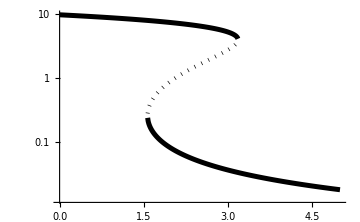

```mathematica
ListLogPlot[oneDT2[[2;;4]],Joined->True,ImageSize->Medium,DataRange->{0,5},PlotStyle->{{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]}},(*PlotRange->{{0,5},{0.01,10}},*)LabelStyle->{14,GrayLevel[0]}]
```

#### x2 bifurcation plot ? (seems not very easy)

```mathematica
x1=NSolve[polx1,Subscript[x, 1]];
```

```mathematica
x2=N[Subscript[x, 2]/.sol1[[1]]/.parSet/.x1]
```

{-(423082. T_2 1^2 (-10.8366-0.0106832 (-65.549-19 1) (-0.0168692-0.331434 (1))))/(89.7725 (17.6201 (1) (0.0231031+267.468 (1))+0.893331 (1) (18+1))-1),-1,1,-1/1}
 |  |  |  |

```mathematica
Length[x2]
```

4

```mathematica
oneDT21=Table[Subscript[x, 2]/.NSolve[{Subscript[x, 2]==x2[[1]]}/.{Subscript[T, 2]->T2},{Subscript[x, 2]}],{T2,0,5,0.01}];
```

```mathematica
oneDT22=Table[Subscript[x, 2]/.NSolve[{Subscript[x, 2]==x2[[2]]}/.{Subscript[T, 2]->T2},{Subscript[x, 2]}],{T2,0,5,0.01}];
```

```mathematica
oneDT23=Table[Subscript[x, 2]/.NSolve[{Subscript[x, 2]==x2[[3]]}/.{Subscript[T, 2]->T2},{Subscript[x, 2]}],{T2,0,5,0.01}];
```

```mathematica
oneDT24=Table[Subscript[x, 2]/.NSolve[{Subscript[x, 2]==x2[[4]]}/.{Subscript[T, 2]->T2},{Subscript[x, 2]}],{T2,0,5,0.01}];
```

```mathematica
oneDT2x2={(*Flatten[oneDT21],*)Flatten[oneDT22],Flatten[oneDT23],Flatten[oneDT24]};
```

```mathematica
Length[oneDT2x2]
```

3

```mathematica
Plot[{ConditionalExpression[x2[[1]],2<Subscript[T, 2]<5],ConditionalExpression[x2[[2]],2<Subscript[T, 2]<5],ConditionalExpression[x2[[3]],0<Subscript[T, 2]<4],ConditionalExpression[Re[x2[[4]]],0<Subscript[T, 2]<5]},{Subscript[T, 2],0,5},PlotRange->{{0,5},{0,11}},PlotStyle->{{Black,Thickness[0.01]},{Dashed,Black,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Thickness[0.01]}},TicksStyle->Automatic,AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["K","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

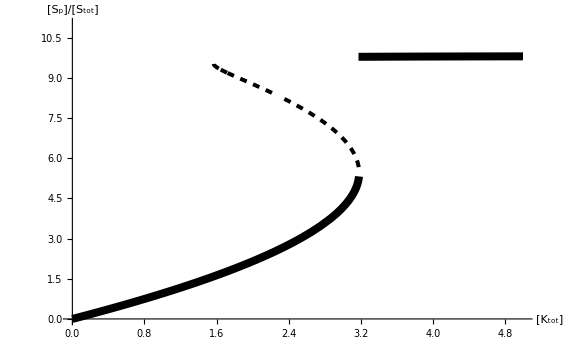

```mathematica
Plot[{ConditionalExpression[x2[[2]],2<Subscript[T, 2]<5],ConditionalExpression[x2[[3]],0<Subscript[T, 2]<5],ConditionalExpression[Re[x2[[4]]],0<Subscript[T, 2]<3.18]},{Subscript[T, 2],0,5},PlotRange->{{0,5},{0,11}},PlotStyle->{{Black,Thickness[0.01]},{Dashed,Black,Thickness[0.005]},{Black,Thickness[0.01]},{Black,Thickness[0.01]}},TicksStyle->Automatic,AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["K","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

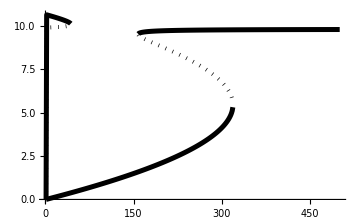

```mathematica
ListPlot[oneDT2x2,Joined->True,ImageSize->Medium,PlotStyle->{{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]}}]
```

```mathematica
ListLogPlot[oneDT2,Joined->True,ImageSize->Medium,DataRange->{0,5},PlotStyle->{{Black,Thickness[0.01]},{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]}},(*PlotRange->{{0,5},{0.01,10}},*)LabelStyle->{14,GrayLevel[0]}]
```

-Graphics-

## Test

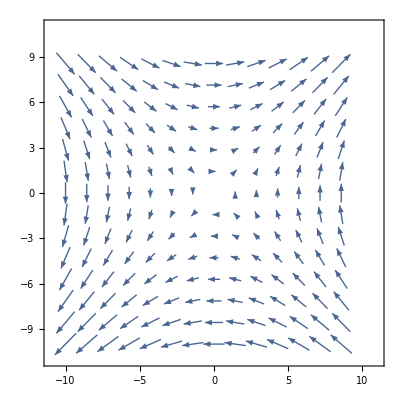

```mathematica
VectorPlot[{y,x},{x,-10,10},{y,-10,10}]
```